### Initialization

Author: Naufer Nusran.  03/29/2019. 
Run Initialization first. 
Edit values for vector magnetic field components in Gauss units in “ShowESR” to see expected NV ensemble ODMR spectrum in MHz x-axis units.

```mathematica
V0={0,0,0}; V1={1/4,1/4,1/4};V2={1/2,1/2,0};V3={1/2,0,1/2};V4={0,1/2,1/2};
D1=Normalize[V0-V1];D2=Normalize[V2-V1];D3=Normalize[V3-V1];D4=Normalize[V4-V1];
P100=Normalize[{1,0,0}];P110=Normalize[{1,1,0}];P111=Normalize[{1,1,1}];


NvPolarAngles[plane_]:=(
dirns={N[ArcCos[D1.plane]/°],N[ArcCos[D2.plane]/°],N[ArcCos[D3.plane]/°],N[ArcCos[D4.plane]/°]};
Table[dirns[[kk]],{kk,1,4}]//TableForm
);

DoubleLF[f_]:=(100-20/π*1/((x-2875-f)^2+ (1)^2)-20/π*1/((x-2875+f)^2+ (1)^2));


gamma=2.003*1.4; (*Field units = G*)
NvFeildSplittings[field_]:=(
Return [{gamma*D1.field,gamma*D2.field,gamma*D3.field,gamma*D4.field}];
);

ShowESR[field_]:=(
temp=NvFeildSplittings[field];
P1=Plot[DoubleLF[temp[[1]]],{x,2675,3075},Frame-> True,PlotStyle-> {Red,Thick,Dashed},PlotRange->All,Axes->None];
P2=Plot[DoubleLF[temp[[2]]],{x,2675,3075},Frame-> True,PlotStyle-> {Green,Thick,Dashed},PlotRange->All,Axes->None];
P3=Plot[DoubleLF[temp[[3]]],{x,2675,3075},Frame-> True,PlotStyle-> {Blue,Thick,Dashed},PlotRange->All,Axes->None];
P4=Plot[DoubleLF[temp[[4]]],{x,2675,3075},Frame-> True,PlotStyle-> {Black,Thick,Dashed},PlotRange->All,Axes->None];
Return[Show[P1,P2,P3,P4]]
)
```

### Plolar angles

#### 100 (CVD)

```mathematica
NvPolarAngles[P100]
```

125.264
54.7356
54.7356
125.264

#### 110 (Thin Natural)

```mathematica
NvPolarAngles[P110]
```

144.736
35.2644
90.
90.

#### 111

```mathematica
NvPolarAngles[P111]
```

180.
70.5288
70.5288
70.5288

### ESR

Author: Naufer Nusran.  03/29/2019. 
Run Initialization first. 
Edit values for vector magnetic field components in Gauss units in “ShowESR” to see expected NV ensemble ODMR spectrum in MHz units x-axis units.

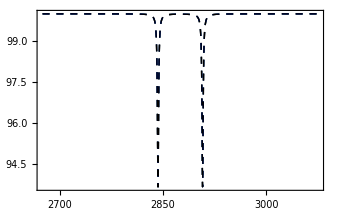

```mathematica
ShowESR[{0,0,20}]
```

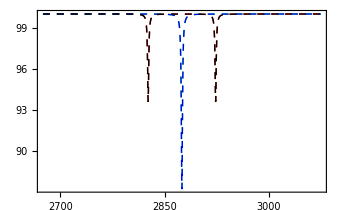

```mathematica
ShowESR[{0,15,15}]
```

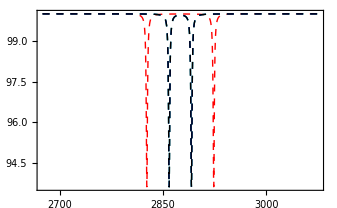

```mathematica
ShowESR[{10,10,10}]
```

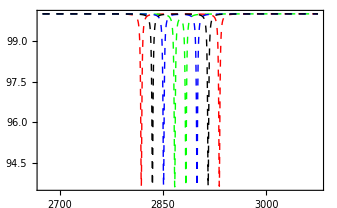

```mathematica
ShowESR[{5,10,20}]
```

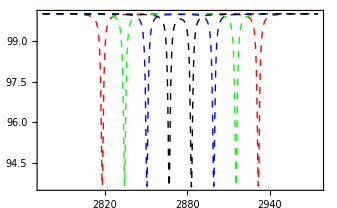

```mathematica
ShowESR[{20,10,5}]
```